## Rectangularize-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Tue 13 Jun 2017 15:06:31
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

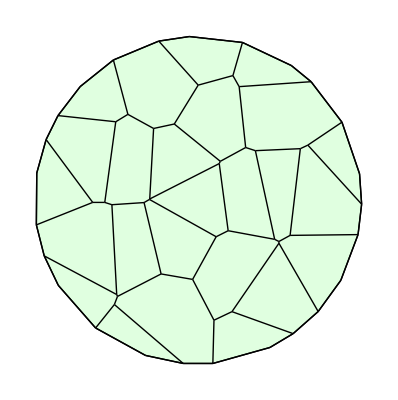

```mathematica
T=TemplateRandomCircularGrid[20, 5];
ShowTissue[T]
```

Projecting vertices ..

Adding corners ..

Merging edges ..

Regularizing mass ..

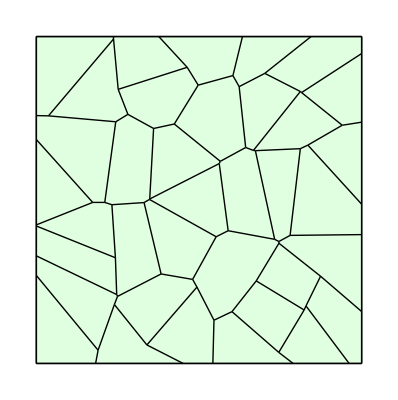

```mathematica
Q=Rectangularize[T];
ShowTissue[Q]
```

```mathematica
NTissueCells/@{T,Q}
```

{25,36}